# MCMC:HW1

Qi Chen(qc586)

## Problem 1

Use rejection sampling to sample from the density function

f(x)∝(-log x)^2(x^3(1-x))^2,0<x<1

Carefully detail the method you use, and provide a figure of the histogram of the samples you obtained. What is the approximate, or actual if you can find it, probability of acceptance.

Solution: For rejection sampling, we can write

f(x)=l(x)h(x)

where

h(x)=(Γ(3+3))/(Γ(3)Γ(3))(x^(3-1)(1-x))^(3-1)=30(x^2(1-x))^2

is the Beta(3,3) pdf. Then

l(x)=𝒩/30(-log x)^2 x

where 𝒩 is the normalization constant. l(x) is bounded by

M=l(ⅇ^-2)=(4𝒩)/(30 ⅇ^2)=(2𝒩)/(15 ⅇ^2)

As

𝒩=108000/919

The rate of acceptance should be

P=1/M≈0.471565

The simulation result(N=1000) gives

P≈0.507

The histogram is as follows:

-Graphics-

```mathematica
Integrate[30 x^2(1-x)^2,{x,0,1}]
```

1

```mathematica
Integrate[(-Log[x])^2 x^3(1-x)^2,{x,0,1}]
```

919/108000

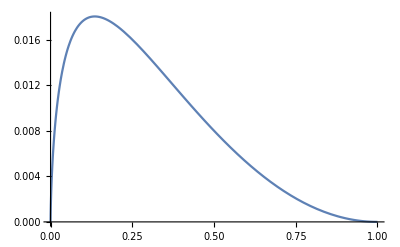

```mathematica
Plot[1/30(Log[x])^2 x,{x,0,1}]
```

```mathematica
N[Exp[-2]]
```

0.135335

```mathematica
N[1/(108000/919*4/(30 ⅇ^2))]
```

0.471565

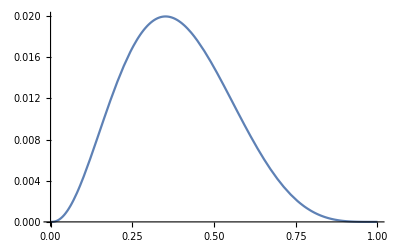

```mathematica
Plot[(-Log[x])^2 x^3(1-x)^2,{x,0,1}]
```

## Problem 2

Use Monte Carlo methods to evaluate the integral

I=∫_0^1 (-log x)^2(x^3(1-x))^(5/2)ⅆx

Describe in detail how you do this. Provide a graphical demonstration that your method has worked. If you fix the Monte Carlo sample size as N = 1000, is there a way to estimate the variance of your (Î)_N.

Solution:

```mathematica
Integrate[(-Log[x])^2 x^3(1-x)^(5/2),{x,0,1}]
```

-(32 π^2)/9009+(64 (7857230824+45045 Log[2] (-187111+90090 Log[2])))/6093243231075

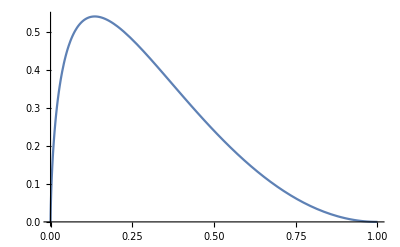

```mathematica
Plot[(Log[x])^2 x,{x,0,1}]
```

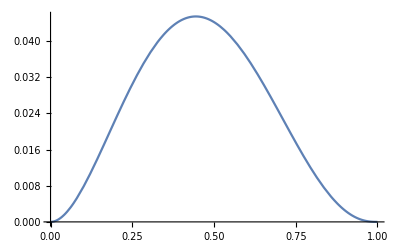

```mathematica
Plot[x^2(1-x)^(5/2),{x,0,1}]
```

The exact result is obtained in R as 0.006587444 with absolute error < 4.1e-07. First we consider direct evaluation:

I=∫_0^1 g(x)f(x)ⅆx

where

f(x)=(Γ(3+7/2))/(Γ(3)Γ(7/2))(x^(3-1)(1-x))^(7/2-1)

g(x)=(Γ(3)Γ(7/2))/(Γ(3+7/2))(-log x)^2 x

The integral can be approximated by generating X_1,X_2,…,X_N~^(i.i.d)Beta(3,7/2) and calculate the average:

(Î)_N=1/N(∑_(i=1))^N g(X_i)≈0.006744701

The variance is evaluated as

Var((Î)_N)=(Var(g(X_i)))/N

which can be estimated by sample variance:

(S((Î)_N))^2=(S(g(X_i)))^2/N=(∑_i (g(X_i)-(Î)_N)^2)/(N(N-1))≈1.198441e-08

The demonstration of variance and convergence is shown in the following graph with the MC result as a function of sample size

-Graphics-

Alternatively, we could use rejection sampling as

f(x)=(-log x)^2(x^3(1-x))^(5/2)=l(x)h(x)

h(x)=(Γ(3+7/2))/(Γ(3)Γ(7/2))(x^(3-1)(1-x))^(7/2-1)

l(x)=(Γ(3)Γ(7/2))/(Γ(3+7/2))(-log x)^2 x

I=∫_0^1 f(x)ⅆx=∫_0^1 ∫_0^1 M^-1 1(u<l(x)/M)h(x).ⅆuⅆx=∫_0^1 ∫_0^1 f(x,u)ⅆuⅆx

where

M=max{l(x)}=(Γ(3)Γ(7/2))/(Γ(3+7/2))4 ⅇ^-2

The acceptance probability is given by

P=I/M⇒I=M×P=(Γ(3)Γ(7/2))/(Γ(3+7/2))4 ⅇ^-2×P≈0.006424227

where P is obtained by numerical simulation.

The variance is evaluated as

Var((Ī)_N)=1/N Var(1(u<l(x)/M))=1/N[E(1(u<l(x)/M))-(E(1(u<l(x)/M)))^2]
=1/N[I/M-(I/M)^2]=1/N(P-P^2)≈0.000249804

The demonstration of variance and convergence is shown in the following graph with the MC result as a function of sample size

-Graphics-

As we can see, the variance is broader than the direct evaluation with beta distribution.

## Problem 3

What is the acceptance probability when sampling a standard normal random variable with density

f(x)=1/(√(2π))ⅇ^(-x^2/2)

using a Cauchy density as proposal; i.e.

h(x)=1/(π(1+x^2))

when using rejection sampling. Verify this using simulation and plot a histogram of 1000 accepted samples.

Solution: We can write f(x) as

f(x)=h(x)l(x)

where

l(x)=√(π/2)ⅇ^(-x^2/2)(1+x^2)

which is bounded by

M=l(±1)=√(2π)ⅇ^(-1/2)

The acceptance probability is given by

P=1/M=1/(√(2π)ⅇ^(-1/2))≈0.657745

The simulation result gives

P≈0.68

The histogram is as follows

-Graphics-

```mathematica
Integrate[1/(π(1+x^2)),{x,-∞,∞}]
```

1

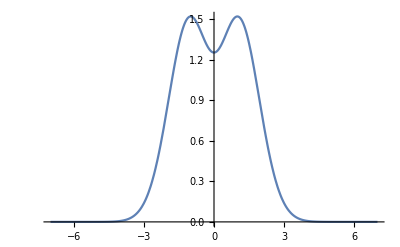

```mathematica
Plot[√(π/2)ⅇ^(-x^2/2)(1+x^2),{x,-7,7},PlotRange->Full]
```

```mathematica
N[1/(√(2π)ⅇ^(-1/2))]
```

0.657745

# Appendix: R-code

# Use rejection sampling to sample from the density function
# f(x)∝(-log x)^2 x^3(1-x)^2,0<x<1

n <- 1000
x <- rbeta(n, shape1=3, shape2=3)
u <- runif(n, min=0, max=1)

sum(u<exp(2)*x*log(x)**2/4)/n

newx <- x[u<exp(2)*x*log(x)**2/4]
hist(newx,freq=FALSE)

# Use Monte Carlo methods to evaluate the integral
# I=\!\(
# \*SubsuperscriptBox[\(∫\), \(0\), \(1\)]\(
#  \*SuperscriptBox[\((\(-log\)\ x)\), \(2\)] 
#  \*SuperscriptBox[\(
#    \*SuperscriptBox[\(x\), \(3\)](1 - x)\), \(5/2\)] ⅆx\)\)

n<-1000

# analytical result
integrand <- function(x) {(log(x))**2*x**3*(1-x)**(5/2)}
integrate(integrand, lower = 0, upper = 1)

# Method I: sampling from beta distribution

x <- rbeta(n, shape1=3, shape2=7/2)
g <- gamma(3)*gamma(7/2)/gamma(3+7/2)*log(x)**2*x
I1 <- sum(g)/n
I1

# demonstration of convergence
I_N1 <- function(n){
  x <- rbeta(n, shape1=3, shape2=7/2)
  g <- gamma(3)*gamma(7/2)/gamma(3+7/2)*log(x)**2*x
  return(sum(g)/n)
}

n = 10:1000
results1 <- lapply(n,I_N1)
plot(n, results1, ylim=c(0.004, 0.01))

# variance estimation
varI1 = sum((g-mean(g))**2)/(n-1)/n
varI1

# Method II: rejection sampling

x <- rbeta(n, shape1=3, shape2=7/2)
u <- runif(n, min=0, max=1)

M=1/(sum(u<exp(2)*x*log(x)**2/4)/n)

I2 <- 4*gamma(3)*gamma(7/2)/(exp(2)*M*gamma(3+7/2))
I2

I_N2 <- function(n){
  x <- rbeta(n, shape1=3, shape2=7/2)
  u <- runif(n, min=0, max=1)
  M=1/(sum(u<exp(2)*x*log(x)**2/4)/n)
  return(4*gamma(3)*gamma(7/2)/(exp(2)*M*gamma(3+7/2)))
}

n = 10:1000
results2 <- lapply(n,I_N2)
plot(n, results2, ylim=c(0.004, 0.01))

# variance estimation
varI2 = 1/n*(1/M-(1/M)**2)
varI2

# What is the acceptance probability when sampling a standard normal random variable with density
# f(x)=1/Sqrt[2π] E^(-x^2/2)
# using a Cauchy density as proposal; i.e.
# h(x)=1/π(1+x^2)
# when using rejection sampling. Verify this using simulation and plot a histogram of 1000 accepted samples.

n <- 1000
x <- rcauchy(n, location=0, scale=1)
u <- runif(n, min=0, max=1)

sum(u < 1/2*exp(-(x**2-1)/2)*(1+x**2))/n

newx <- x[u<1/2*exp(-(x**2-1)/2)*(1+x**2)]
hist(newx,freq=FALSE)